# Tension of the E_G statistic and RSD data with Planck/ΛCDM and implications for weakening gravity. Numerical Analysis and Construction Figures File

## Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
(* In order to use the Needs["ErrorBarLogPlots`"] command you need to install the "Error Bar Log Plots" package which can be installed directly from the zip file "ErrorBarLogPlots.zip" or you can download it from http://library.wolfram.com/infocenter/MathSource/6747/*)

Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol,Part::partw,NonlinearModelFit::cvmit];
```

## Parameter values

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"] 

(* Planck parameter Values for Planck18 *)

ompl=0.3153;
nn=2;
mm=2 ;
omplerr=0.0073;
h0pl=0.6727;
h0plerr=0.0066;
σ8pl=0.8111;
σ8plerr=0.006;
```

## Datasets

```mathematica
(* Data fσ8  *)

datafσ8={{0.02,0.314,0.048},{0.25,0.3512,0.0583},{0.44,0.413,0.08},{0.6,0.39,0.063},{0.73,0.437,0.072},{0.18,0.36,0.09},{0.15,0.49,0.145},{0.1,0.37,0.13},{1.4,0.482,0.116},{0.38,0.497,0.045},{0.51,0.458,0.038},{0.61,0.436,0.034},{1.05,0.28,0.08},{0.32,0.427,0.056},{0.727,0.296,0.0765},{0.02,0.428,0.0465},{0.001,0.505,0.085},{0.31,0.384,0.083},{0.36,0.409,0.098},{0.4,0.461,0.086},{0.44,0.426,0.062},{0.48,0.458,0.063},{0.52,0.483,0.075},{0.56,0.472,0.063},{0.59,0.452,0.061},{0.64,0.379,0.054},{0.978,0.379,0.176},{1.23,0.385,0.099},{1.526,0.342,0.07},{1.944,0.364,0.106},{0.60,0.49,0.12},{0.86,0.46,0.09},{0.57,0.501,0.051},{0.03,0.404,0.0815},{0.72,0.454,0.139}} ;

(* Data fσ8 with fiducial cosmology *)

datafσ8fid={{0.02,0.314,0.048,0.266},{0.25,0.3512,0.0583,0.25},{0.44,0.413,0.08,0.27},{0.6,0.39,0.063,0.27},{0.73,0.437,0.072,0.27},{0.18,0.36,0.09,0.27},{0.15,0.49,0.145,0.31},{0.1,0.37,0.13,0.3},{1.4,0.482,0.116,0.27},{0.38,0.497,0.045,0.31},{0.51,0.458,0.038,0.31},{0.61,0.436,0.034,0.31},{1.05,0.28,0.08,0.308},{0.32,0.427,0.056,0.31},{0.727,0.296,0.0765,0.31},{0.02,0.428,0.0465,0.3},{0.001,0.505,0.085,0.31},{0.31,0.384,0.083,0.307},{0.36,0.409,0.098,0.307},{0.4,0.461,0.086,0.307},{0.44,0.426,0.062,0.307},{0.48,0.458,0.063,0.307},{0.52,0.483,0.075,0.307},{0.56,0.472,0.063,0.307},{0.59,0.452,0.061,0.307},{0.64,0.379,0.054,0.307},{0.978,0.379,0.176,0.31},{1.23,0.385,0.099,0.31},{1.526,0.342,0.07,0.31},{1.944,0.364,0.106,0.31},{0.60,0.49,0.12,0.31},{0.86,0.46,0.09,0.31},{0.57,0.501,0.051,0.307},{0.03,0.404,0.0815,0.3121},{0.72,0.454,0.139,0.31}} ;
```

```mathematica
(* Data  Eg(z)*)

dataeg={{0.267,0.43,0.13},{0.305,0.27,0.08},{0.32,0.4,0.09},{0.554,0.26,0.07},{0.57,0.31,0.06},{0.57,0.3,0.07},{0.6,0.16,0.09},{0.86,0.09,0.07}};

dataegb={{0.267,0.43,0.13},{0.305,0.27,0.08},{0.32,0.4,0.09},{0.554,0.26,0.07},{0.57,0.31,0.06},{0.575,0.3,0.07},{0.6,0.16,0.09},{0.86,0.09,0.07}};
```

## Theoretical Expressions

```mathematica
(* The fσ8  and the Subscript[E, G] observables *)

H[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)))
dLh[a_,om_,w_]:=2/(a √om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)])
amin=0.001;

Geff[a_,ga_,n_]:=1+ga(1-a)^n-ga(1-a)^(2n);
Gl[z_,gb_,m_]:=1+gb(z/(1+z))^m-gb(z/(1+z))^(2m);

dsol[om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ]:=(dsol[om,w,ga,n]=Module[{a},NDSolve[{-((3 om d[a] Geff[a,ga,n])/(2 a^5  H[a,w,om]^2))+d'[a] (3/a+D[H[a,w,om],a]/H[a,w,om])+d''[a]==0,d[amin]==amin,d'[amin]==1},d,{a,amin,1}][[1]]])

Da[a_,om_,w_,ga_,n_]:=d[a]/.dsol[om,w,ga,n]
fa[aa_,om_,w_,ga_,n_]:=a d'[a]/d[a]/.a->aa/.dsol[om,w,ga,n]

fσ8geff[a_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w,ga,n])/Da[1,om,w,ga,n] fa[aa,om,w,ga,n]/.aa->a
fσ8z[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w,ga,n])/Da[1,om,w,ga,n] fa[aa,om,w,ga,n]/.aa->1/(1+z)

ffz[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ]:=fa[aa,om,w,ga,n]/.aa->1/(1+z)

ratio1[z_,w_,om_,omfid_]:=((H[a,w,om] dLh[a,om,w])/(H[a,-1,omfid] dLh[a,omfid,-1]))^(-1)/.a->1/(1+z);



eg[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,gb_?NumberQ,n_?NumberQ,m_?NumberQ]:=(om   Gl[z,gb,m]) /ffz[z,om,w,ga,n]
```

```mathematica
(* Sigma Difference of terms*)

dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
nsig[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
```

## Figure 9

```mathematica
(* Covariance Matrix for data  fσ8*)


Cijwigglez=10^-3*({{6.400, 2.570, 0.000}, {2.570, 3.969, 2.540}, {0.000, 2.540, 5.184}});

Wigglez={10,11,12};
Cijfσ8=DiagonalMatrix[datafσ8fid[[All,3]]^2];
Cijfσ8[[Wigglez,Wigglez]]=Cijwigglez;
InvCijfσ8=Inverse[Cijfσ8];
```

```mathematica
(* Correlated χ^2 term for fσ8 with fiducial cosmology *)

vecfσ8[data_,w_,om_,ga_,n_,σ8_]:=Table[data[[i,2]]-ratio1[data[[i,1]],w,om,data[[i,4]]]fσ8geff[1/(1+data[[i,1]]),om,w,ga,n,σ8],{i,1,Length[data]}]
chi2fid[data_,w_,om_,ga_,n_,σ8_]:=vecfσ8[data,w,om,ga,n,σ8].InvCijfσ8.vecfσ8[data,w,om,ga,n,σ8]
```

```mathematica
(* Minimization of χ^2 for data fσ8 with fiducial cosmology , with marginalization over w *)

intchi2w[data_,om_,ga_,n_,σ8_]:=Sum[Exp[-chi2fid[data,w,om,ga,n,σ8]/2],{w,-1.5,-0.5,0.1},GenerateConditions->False]
chi2fidmargw[data_,om_,ga_,n_,σ8_]:=-Log[intchi2w[data,om,ga,n,σ8]^2]
chi2minfσ8margw=FindMinimum[chi2fidmargw[datafσ8fid,om,0,0,σ8],{om,0.27},{σ8,0.8}]
```

{17.5966,{om→0.300376,σ8→0.736932}}

```mathematica
(* Minimization of χ^2 for data fσ8 with fiducial cosmology , best fit of w*)

chi2minfσ8w=FindMinimum[chi2fid[datafσ8fid,w,om,0,0,σ8],{om,0.30,0.31},{w,-1,-0.9},{σ8,0.8,0.81}]
```

{19.623,{om→0.290239,w→-0.944911,σ8→0.761857}}

```mathematica
(* Minimization of χ^2 for data fσ8 with fiducial cosmology, with w=-1 *)

chi2minfσ8gr=FindMinimum[chi2fid[datafσ8fid,-1,om,0,0,σ8],{om,0.30,0.31},{σ8,0.8,0.81}]
```

{19.6582,{om→0.29311,σ8→0.749575}}

```mathematica
{19.658175292868442,{om->0.2931099385298735,σ8->0.749575153099672}}
```

{19.6582,{om→0.29311,σ8→0.749575}}

```mathematica
(* Tension level in the   space (Subscript[Ω, 0m], σ8) with fiducial cosmology , with marginalization over w *)

dchifσ8omσ8margw=chi2fidmargw[datafσ8fid,ompl,0,0,σ8pl]-chi2minfσ8margw[[1]];
nsigfσ8omσ8margw[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,3}][[1,2]]
nsigfσ8omσ8margw[dchifσ8omσ8margw,2]
```

1.00484

```mathematica
(* Tension level in the   space (Subscript[Ω, 0m], σ8) with fiducial cosmology , best fit of w *)

dchifσ8omσ8w=chi2fid[datafσ8fid,chi2minfσ8w[[2,2,2]],ompl,0,0,σ8pl]-chi2minfσ8w[[1]];
nsigfσ8omσ8w[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,3}][[1,2]]
nsigfσ8omσ8w[dchifσ8omσ8w,3]
```

2.38381

```mathematica
(* Tension level in the   space (Subscript[Ω, 0m], σ8) with fiducial cosmology , with w=-1  *)

dchifσ8omσ8gr=chi2fid[datafσ8fid,-1,ompl,0,0,σ8pl]-chi2minfσ8gr[[1]];
nsigfσ8omσ8gr[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,3}][[1,2]]
nsigfσ8omσ8gr[dchifσ8omσ8gr,2]
```

2.73266

## Figure 9 (Fσ8 data)

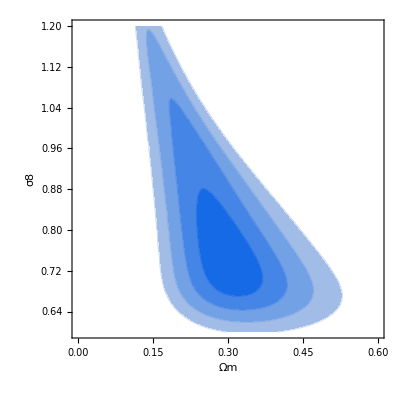

```mathematica
(* 1σ-4σ confidence contour in  space (Subscript[Ω, 0m], σ8) , with  marginalization over w,  including the fiducial correction factor*)

contour2fσ8margw=ContourPlot[chi2fidmargw[datafσ8fid,om,0,0,σ8],{om,0.,0.6},{σ8,0.6,1.2},FrameLabel->{"Ωm","σ8"},Contours->{chi2minfσ8margw[[1]]+dchi[1,2],chi2minfσ8margw[[1]]+dchi[2,2],chi2minfσ8margw[[1]]+dchi[3,2],chi2minfσ8margw[[1]]+dchi[4,2]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],White}]
```

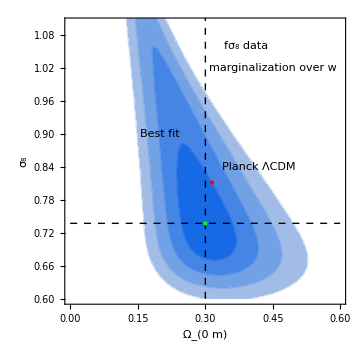

```mathematica
cont2fσ8margw=Show[contour2fσ8margw,Graphics[{Inset["Best fit",{0.2,0.9},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8 data",{0.39,1.06},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["marginalization over w ",{0.45,1.02},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.42,0.84},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.,0.6},{0.6,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{chi2minfσ8margw[[2,1,2]],0.6},{chi2minfσ8margw[[2,1,2]],1.2}}]},{Dashed,Line[{{0.,chi2minfσ8margw[[2,2,2]]},{0.6,chi2minfσ8margw[[2,2,2]]}}]},{PointSize[Large],Red,Point[{0.3153,0.8111}]},{PointSize[Large],Green,Point[{chi2minfσ8margw[[2,1,2]],chi2minfσ8margw[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

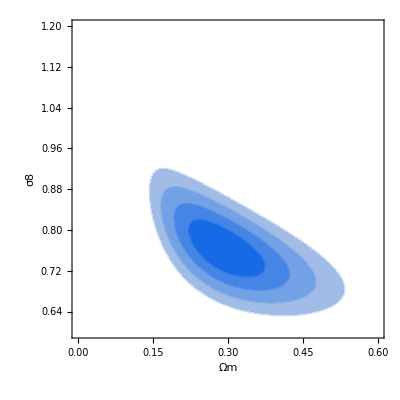

```mathematica
(* 1σ -4σ confidence contour in 2D space (Subscript[Ω, 0m], σ8) , best fit of w *)

contour2fσ8w=ContourPlot[chi2fid[datafσ8fid,chi2minfσ8w[[2,2,2]],om,0,0,σ8],{om,0.,0.6},{σ8,0.6,1.2},FrameLabel->{"Ωm","σ8"},Contours->{chi2minfσ8w[[1]]+dchi[1,3],chi2minfσ8w[[1]]+dchi[2,3],chi2minfσ8w[[1]]+dchi[3,3],chi2minfσ8w[[1]]+dchi[4,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],White}]
```

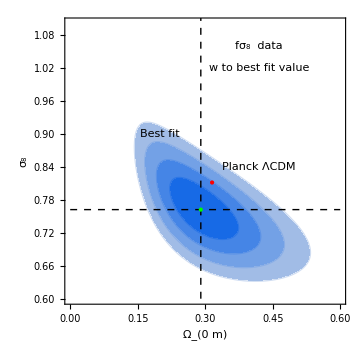

```mathematica
cont2fσ8w=Show[contour2fσ8w,Graphics[{Inset["Best fit",{0.2,0.9},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8  data   ",{0.42,1.06},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["w to best fit value",{0.42,1.02},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.42,0.84},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0,0.6},{0.6,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{chi2minfσ8w[[2,1,2]],0.6},{chi2minfσ8w[[2,1,2]],1.2}}]},{Dashed,Line[{{0.,chi2minfσ8w[[2,3,2]]},{0.6,chi2minfσ8w[[2,3,2]]}}]},{PointSize[Large],Red,Point[{0.3153,0.8111}]},{PointSize[Large],Green,Point[{chi2minfσ8w[[2,1,2]],chi2minfσ8w[[2,3,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

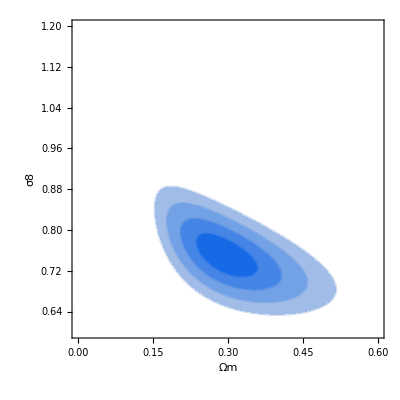

```mathematica
(* 1σ-4σ confidence contour in 2D space (Subscript[Ω, 0m], σ8) (with w=-1, Subscript[g, a]=0) including the fiducial correction factor*)

contour2fσ8gr=ContourPlot[chi2fid[datafσ8fid,-1,om,0,0,σ8],{om,0.,0.6},{σ8,0.6,1.2},FrameLabel->{"Ωm","σ8"},Contours->{chi2minfσ8gr[[1]]+dchi[1,2],chi2minfσ8gr[[1]]+dchi[2,2],chi2minfσ8gr[[1]]+dchi[3,2],chi2minfσ8gr[[1]]+dchi[4,2]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],White}]
```

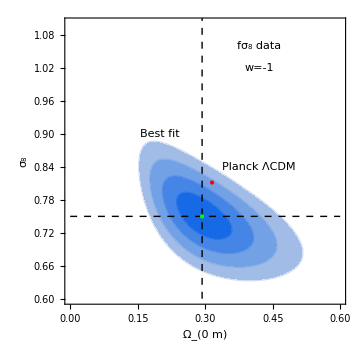

```mathematica
cont2fσ8gr=Show[contour2fσ8gr,Graphics[{Inset["Best fit",{0.2,0.9},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8 data",{0.42,1.06},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["w=-1 ",{0.42,1.02},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.42,0.84},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.,0.6},{0.6,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{chi2minfσ8gr[[2,1,2]],0.6},{chi2minfσ8gr[[2,1,2]],1.2}}]},{Dashed,Line[{{0.,chi2minfσ8gr[[2,2,2]]},{0.6,chi2minfσ8gr[[2,2,2]]}}]},{PointSize[Large],Red,Point[{0.3153,0.8111}]},{PointSize[Large],Green,Point[{chi2minfσ8gr[[2,1,2]],chi2minfσ8gr[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

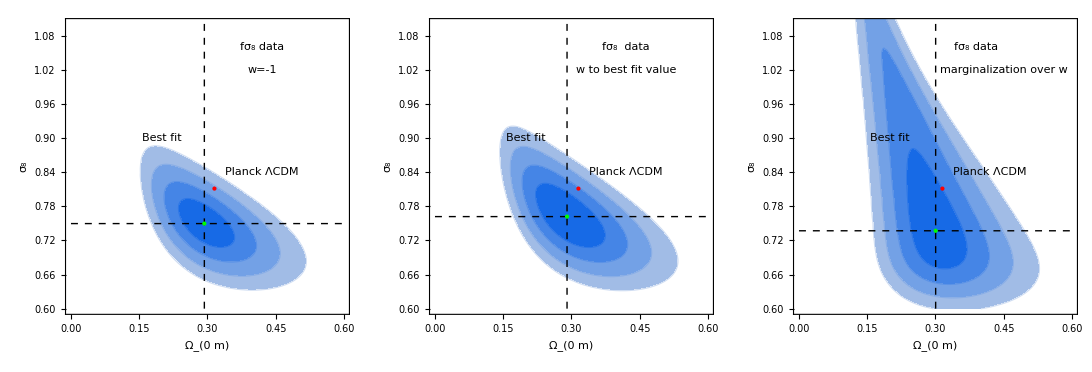

```mathematica
figw=GraphicsGrid[{{cont2fσ8gr,cont2fσ8w,cont2fσ8margw}},Spacings->0]
```

## Figure 9 (Fσ8-Eg data)

```mathematica
(* Covariance Matrix for data  fσ8*)


Cijwigglez=10^-3*({{6.400, 2.570, 0.000}, {2.570, 3.969, 2.540}, {0.000, 2.540, 5.184}});

Wigglez={10,11,12};
Cijf=DiagonalMatrix[datafσ8fid[[All,3]]^2];
Cijf[[Wigglez,Wigglez]]=Cijwigglez;
InvCijf=Inverse[Cijf];

Cijf//MatrixForm;
(* Covariance Matrix for data  Eg*)

Cije=DiagonalMatrix[dataeg[[All,3]]^2];

InvCije=Inverse[Cije];

Cije//MatrixForm;
```

```mathematica
(* Correlated χ^2 term for Eg*)
 
vec1[data1_,w_,om_,ga_,gb_,n_,m_]:=Table[(data1[[i,2]]-eg[data1[[i,1]],om,w,ga,gb,n,m]),{i,1,Length[data1]}];
chi2e[data1_,w_,om_,ga_,gb_,n_,m_]:=vec1[data1,w,om,ga,gb,n,m].InvCije.vec1[data1,w,om,ga,gb,n,m]


(* Correlated χ^2 term for fσ8 with fiducial cosmology *)
vec2[data2_,w_,om_,ga_,n_,σ8_]:=Table[data2[[j,2]]-ratio1[data2[[j,1]],w,om,data2[[j,4]]]fσ8geff[1/(1+data2[[j,1]]),om,w,ga,n,σ8],{j,1,Length[data2]}]
chi2f[data2_,w_,om_,ga_,n_,σ8_]:=vec2[data2,w,om,ga,n,σ8].InvCijf.vec2[data2,w,om,ga,n,σ8]
```

```mathematica
(* Correlated χ^2 term for Eg  and fσ8 with fiducial cosmology *)

chi2[data1_,data2_,w_,om_,ga_,gb_,n_,m_,σ8_]:=chi2f[data2,w,om,ga,n,σ8]+chi2e[data1,w,om,ga,gb,n,m]
```

```mathematica
(* Minimization of χ^2 for data fσ8 and Eg with fiducial cosmology , with marginalization over w *)

intchi2few[data1_,data2_,om_,ga_,gb_,n_,m_,σ8_]:=Sum[Exp[-chi2[data1,data2,w,om,ga,gb,n,m,σ8]/2],{w,-1.5,-0.5,0.1},GenerateConditions->False]
chi2femargw[data1_,data2_,om_,ga_,gb_,n_,m_,σ8_]:=-Log[intchi2few[data1,data2,om,ga,gb,n,m,σ8]^2]
chi2minfemargw=FindMinimum[chi2femargw[dataeg,datafσ8fid,om,0,0,0,0,σ8],{om,0.30,0.31},{σ8,0.8,0.81}]
```

{33.0014,{om→0.234199,σ8→0.712609}}

```mathematica
(* Minimization of χ^2 for data with fiducial cosmology , w=-1 *)

chi2minfegr=FindMinimum[chi2[dataeg,datafσ8fid,-1,om,0,0,0,0,σ8],{om,0.3,0.31},{σ8,0.80,0.81}]
```

{36.3074,{om→0.212906,σ8→0.790748}}

```mathematica
(* Minimization of χ^2 for data with fiducial cosmology , best fit of w *)

chi2minfew=FindMinimum[chi2[dataeg,datafσ8fid,w,om,0,0,0,0,σ8],{om,0.3,0.31},{w,-1,-1.1},{σ8,0.80,0.81}]
```

{35.0555,{om→0.231782,w→-1.2923,σ8→0.718089}}

```mathematica
(* Tension level in the  parameter space (Subscript[Ω, 0m],σ8) with fiducial, with marginalization over w *)

dchifeomσ8margw=chi2femargw[dataeg,datafσ8fid,ompl,0,0,2,2,σ8pl]-chi2minfemargw[[1]];
nsigfeomσ8margw[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,6},AccuracyGoal->2][[1,2]]
nsigfeomσ8margw[dchifeomσ8margw,2]
```

5.37385

```mathematica
(* Tension level in the  parameter space (Subscript[Ω, 0m],σ8) with fiducial cosmology *)

dchifeomσ8w=chi2[dataeg,datafσ8fid,chi2minfew[[2,2,2]],ompl,0,0,2,2,σ8pl]-chi2minfew[[1]];
nsigfeomσ8w[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,6},AccuracyGoal->2][[1,2]]
nsigfeomσ8w[dchifeomσ8w,3]
```

5.91775

```mathematica
(* Tension level in the  parameter space (Subscript[Ω, 0m],σ8) with fiducial cosmology *)

dchifeomσ8gr=chi2[dataeg,datafσ8fid,-1,ompl,0,0,2,2,σ8pl]-chi2minfegr[[1]];
nsigfeomσ8gr[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,6},AccuracyGoal->2][[1,2]]
nsigfeomσ8gr[dchifeomσ8gr,2]
```

5.24388

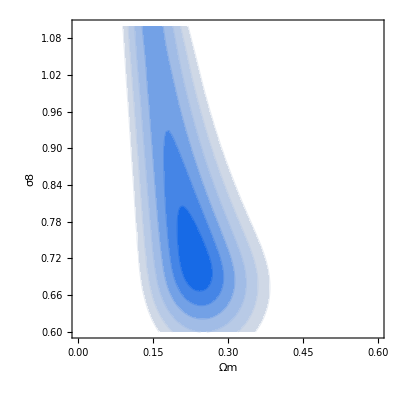

```mathematica
(* 1σ-6σ confidence contour in  space (Subscript[Ω, 0m], σ8) , with  marginalization over w  *)

contour2femargw=ContourPlot[chi2femargw[dataeg,datafσ8fid,om,0,0,0,0,σ8],{om,0.0,0.6},{σ8,0.6,1.1},FrameLabel->{"Ωm","σ8"},Contours->{chi2minfemargw[[1]]+dchi[1,2],chi2minfemargw[[1]]+dchi[2,2],chi2minfemargw[[1]]+dchi[3,2],chi2minfemargw[[1]]+dchi[4,2],chi2minfemargw[[1]]+dchi[5,2],chi2minfemargw[[1]]+dchi[6,2]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],White}]
```

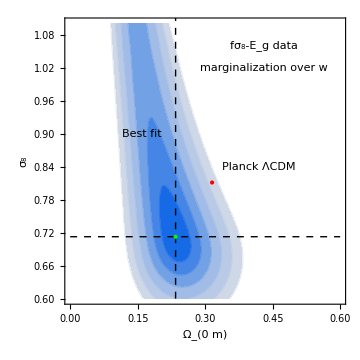

```mathematica
cont2femargw=Show[contour2femargw,Graphics[{Inset["Best fit",{0.16,0.9},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8-E_g data ",{0.43,1.06},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset[" marginalization over w",{0.43,1.02},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.42,0.84},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.,0.6},{0.6,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{chi2minfemargw[[2,1,2]],0.6},{chi2minfemargw[[2,1,2]],1.2}}]},{Dashed,Line[{{0.,chi2minfemargw[[2,2,2]]},{0.6,chi2minfemargw[[2,2,2]]}}]},{PointSize[Large],Red,Point[{0.3153,0.8111}]},{PointSize[Large],Green,Point[{chi2minfemargw[[2,1,2]],chi2minfemargw[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

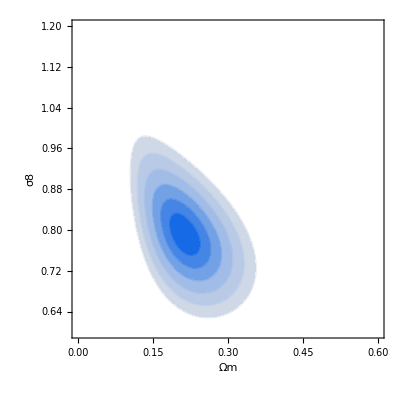

```mathematica
(* 1σ-6σ confidence contour in space (Subscript[Ω, 0m], σ8) , with w=-1  *)

contour2fegr=ContourPlot[chi2[dataeg,datafσ8fid,-1,om,0,0,0,0,σ8],{om,0.,0.6},{σ8,0.6,1.2},FrameLabel->{"Ωm","σ8"},Contours->{chi2minfegr[[1]]+dchi[1,2],chi2minfegr[[1]]+dchi[2,2],chi2minfegr[[1]]+dchi[3,2],chi2minfegr[[1]]+dchi[4,2],chi2minfegr[[1]]+dchi[5,2],chi2minfegr[[1]]+dchi[6,2]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],White}]
```

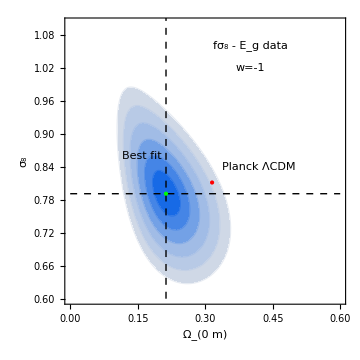

```mathematica
cont2fegr=Show[contour2fegr,Graphics[{Inset["Best fit",{0.16,0.86},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8 - E_g data   ",{0.4,1.06},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset[" w=-1",{0.4,1.02},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.42,0.84},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.,0.6},{0.6,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{chi2minfegr[[2,1,2]],0.6},{chi2minfegr[[2,1,2]],1.2}}]},{Dashed,Line[{{0.,chi2minfegr[[2,2,2]]},{0.6,chi2minfegr[[2,2,2]]}}]},{PointSize[Large],Red,Point[{0.3153,0.8111}]},{PointSize[Large],Green,Point[{chi2minfegr[[2,1,2]],chi2minfegr[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

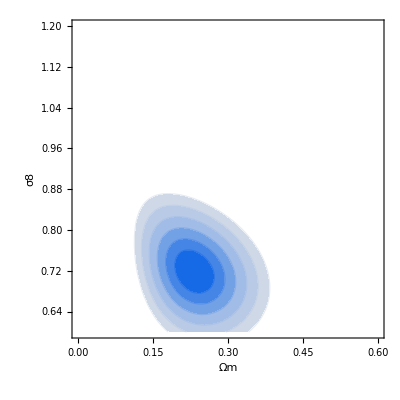

```mathematica
(* 1σ-6σ confidence contour in 2D space (Subscript[Ω, 0m], σ8) , best fit of w *)

contour2few=ContourPlot[chi2[dataeg,datafσ8fid,chi2minfew[[2,2,2]],om,0,0,0,0,σ8],{om,0.,0.6},{σ8,0.6,1.2},FrameLabel->{"Ωm","σ8"},Contours->{chi2minfew[[1]]+dchi[1,3],chi2minfew[[1]]+dchi[2,3],chi2minfew[[1]]+dchi[3,3],chi2minfew[[1]]+dchi[4,3],chi2minfew[[1]]+dchi[5,3],chi2minfew[[1]]+dchi[6,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],White}]
```

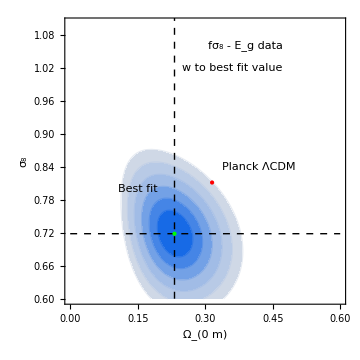

```mathematica
cont2few=Show[contour2few,Graphics[{Inset["Best fit",{0.15,0.8},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8 - E_g data   ",{0.39,1.06},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["w to best fit value",{0.36,1.02},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.42,0.84},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.,0.6},{0.6,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{chi2minfew[[2,1,2]],0.6},{chi2minfew[[2,1,2]],1.2}}]},{Dashed,Line[{{0.,chi2minfew[[2,3,2]]},{0.6,chi2minfew[[2,3,2]]}}]},{PointSize[Large],Red,Point[{0.3153,0.8111}]},{PointSize[Large],Green,Point[{chi2minfew[[2,1,2]],chi2minfew[[2,3,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

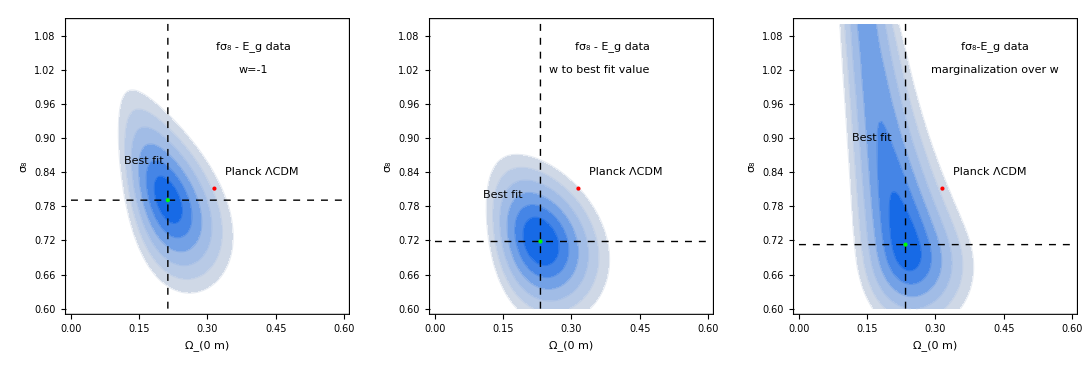

```mathematica
figfew=GraphicsGrid[{{cont2fegr,cont2few,cont2femargw}},Spacings->0]
```

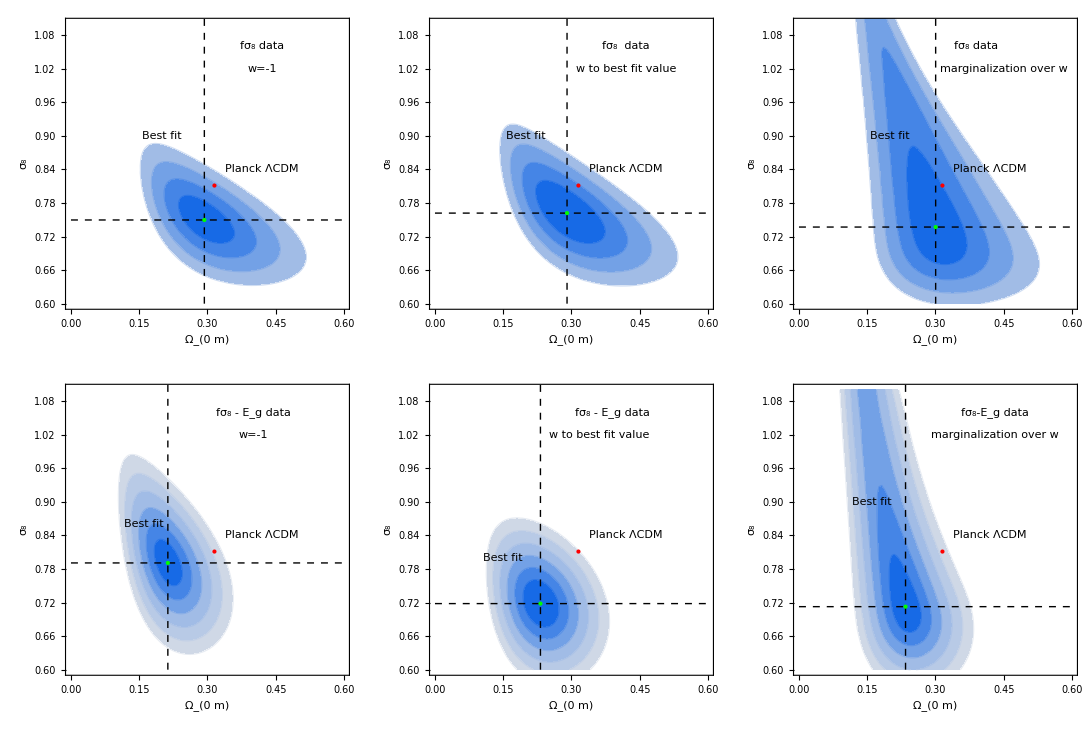

```mathematica
figsuballw=GraphicsGrid[{{cont2fσ8gr,cont2fσ8w,cont2fσ8margw},{cont2fegr,cont2few,cont2femargw}},Spacings->0]
Export[NotebookDirectory[]<>"figfewsub63.pdf",figsuballw,ImageResolution->1000];
```